```mathematica
f[x_, d_, σ_] := 1/(√(2π)σ)Exp[-(d-x)^2/(2 σ^2)]
```

```mathematica
prob[d_, σ_, x0_, xtrue_:0] = Integrate[f[x,d,σ], {x,-x0,xtrue}]/Integrate[f[x,d,σ], {x, -x0, x0}]
```

(Erf[(d+x0)/(√2 σ)]-Erf[(d-xtrue)/(√2 σ)])/(-Erf[(d-x0)/(√2 σ)]+Erf[(d+x0)/(√2 σ)])

```mathematica
prob[d,σ,x0]
```

(-Erf[d/(√2 σ)]+Erf[(d+x0)/(√2 σ)])/(-Erf[(d-x0)/(√2 σ)]+Erf[(d+x0)/(√2 σ)])

```mathematica
uniftest[σ_, x0_, N_]:= Histogram[prob[#, σ, x0] & /@ RandomVariate[NormalDistribution[0.0,σ],N]];
```

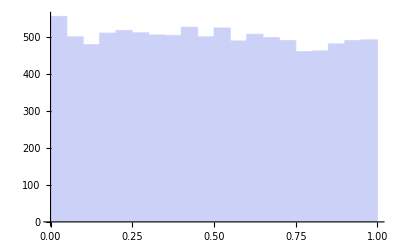

```mathematica
uniftest[0.01, 0.1, 10000]
```

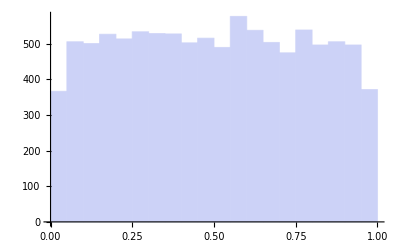

```mathematica
uniftest[0.04, 0.1, 10000]
```

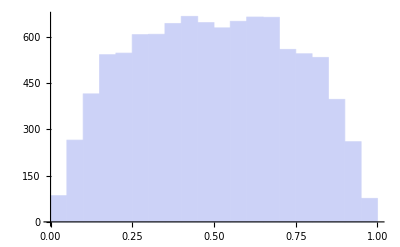

```mathematica
uniftest[0.07, 0.1, 10000]
```

## Test by putting in prior sampling of x

Cook, Gelman & Rubin (2006, Journal of Computational and Graphical Statistics) suggest a way of testing posterior distributions. Unlike the cases we just did, this requires sampling the true value from the prior distribution and then generating the data. In this case, P(x < x_true) is Uniform(0,1). Doing this below fixes the issues we saw above.

```mathematica
(* The function below draws a true value from -x0 to x0 and then a Gaussian with width σ).
```

```mathematica
data2[σ_, x0_, N_]:=  MapThread[{#1, #1+#2}&, {RandomReal[{-x0,x0}, N],RandomVariate[NormalDistribution[0.0,σ],N]}];
```

```mathematica
(* Now apply the test, taking into account the true value as well *)
```

```mathematica
uniftest2[σ_, x0_, N_]:=Histogram[prob[#[[2]], σ, x0, #[[1]]]&/@ data2[σ,x0, N]];
```

```mathematica
(* Note that this is now uniform! *)
```

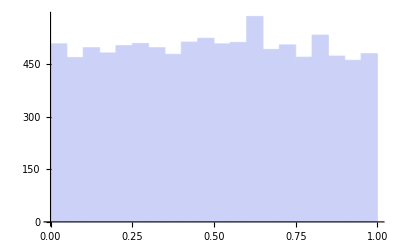

```mathematica
uniftest2[0.07, 0.1, 10000]
```